```mathematica
AB2Roots = z/. Solve[z^(2) - (1 + (3/2)*r)*z + (1/2)*r == 0, z, Complexes]
```

{1/4 (2+3 r-√(4+4 r+9 r^2)),1/4 (2+3 r+√(4+4 r+9 r^2))}

```mathematica
AB2Roots1 = AB2Roots[[1]]
AB2Roots2 = AB2Roots[[2]]
```

1/4 (2+3 r-√(4+4 r+9 r^2))

1/4 (2+3 r+√(4+4 r+9 r^2))

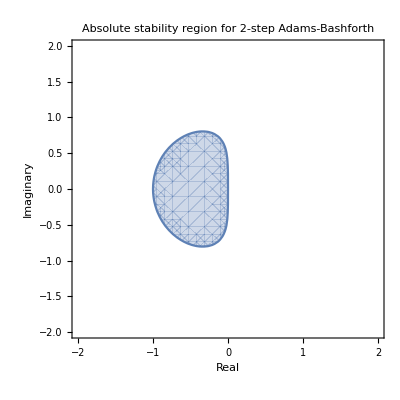

```mathematica
ComplexRegionPlot[{Abs[AB2Roots1] <=1 && Abs[AB2Roots2] <= 1}, {r, 2}, FrameLabel->{"Real", "Imaginary"}, PlotLabel->"Absolute stability region for 2-step Adams-Bashforth"]
```

```mathematica
AB3Roots = z /. Solve[z^(3) - (1+(23/12)*r)*z^(2) + (4/3)*r*z - (5/12)*r==0,z,Complexes]
```

{1/36 (12+23 r)-(4 (-1+r/6-(529 r^2)/144))/((1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3))+1/36 (1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3),1/36 (12+23 r)+(2 (1+ⅈ √3) (-1+r/6-(529 r^2)/144))/((1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3))-1/72 (1-ⅈ √3) (1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3),1/36 (12+23 r)+(2 (1-ⅈ √3) (-1+r/6-(529 r^2)/144))/((1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3))-1/72 (1+ⅈ √3) (1728+9288 r-828 r^2+12167 r^3+108 √r √(2880+4308 r+3228 r^2+8993 r^3))^(1/3)}

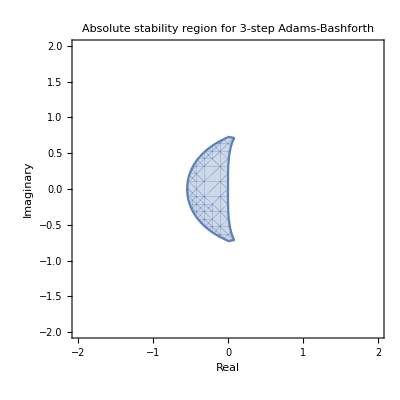

```mathematica
ComplexRegionPlot[{Abs[AB3Roots[[1]]] <= 1&&Abs[AB3Roots[[2]]] <= 1 && Abs[AB3Roots[[3]]] <= 1}, {r, 2},FrameLabel->{"Real", "Imaginary"}, PlotLabel->"Absolute stability region for 3-step Adams-Bashforth"]
```

```mathematica
AM2Roots = z /. Solve[(1-(5/12)*r)*z^(2)-(1+(2/3)*r)*z+(1/12)*r==0,z,Complexes]
```

{(-6-4 r-√3 √(12+12 r+7 r^2))/(-12+5 r),(-6-4 r+√3 √(12+12 r+7 r^2))/(-12+5 r)}

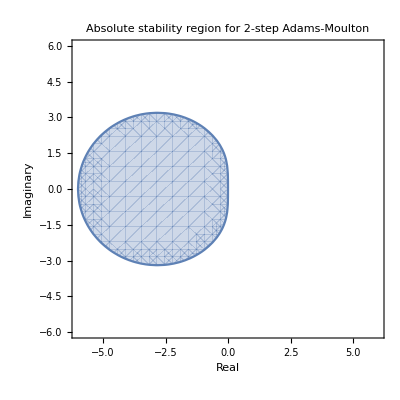

```mathematica
ComplexRegionPlot[{Abs[AM2Roots[[1]]] <= 1&&Abs[AM2Roots[[2]]] <= 1}, {r, 6},FrameLabel->{"Real", "Imaginary"}, PlotLabel->"Absolute stability region for 2-step Adams-Moulton"]
```

```mathematica
BDF2Roots = z /. Solve[(1-(2/3)*r)*z^(2)-(4/3)*z+(1/3)==0,z,Complexes]
```

{(-2-√(1+2 r))/(-3+2 r),(-2+√(1+2 r))/(-3+2 r)}

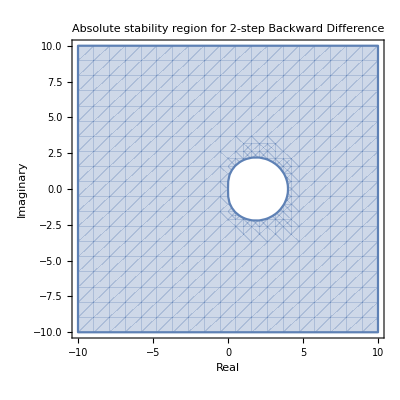

```mathematica
ComplexRegionPlot[{Abs[BDF2Roots[[1]]] <= 1&&Abs[BDF2Roots[[2]]] <= 1}, {r, 10},FrameLabel->{"Real", "Imaginary"}, PlotLabel->"Absolute stability region for 2-step Backward Difference"]
```

```mathematica
BDF3Roots = z /. Solve[(1-(6/11)*r)*z^(3)-(18/11)*z^(2)+(9/11)*z-(2/11)==0,z,Complexes]
```

{6/(11-6 r)-(-27-162 r)/(9 (11-6 r) (40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))+((40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))/(11-6 r),6/(11-6 r)+((1+ⅈ √3) (-27-162 r))/(18 (11-6 r) (40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))-((1-ⅈ √3) (40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))/(2 (11-6 r)),6/(11-6 r)+((1-ⅈ √3) (-27-162 r))/(18 (11-6 r) (40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))-((1+ⅈ √3) (40+30 r+36 r^2+√(1573+1914 r+864 r^2-3672 r^3+1296 r^4))^(1/3))/(2 (11-6 r))}

LessEqual::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 5/11-3/(11 (40+11 √13)^(1/3))-1/11 (40+11 √13)^(1/3).

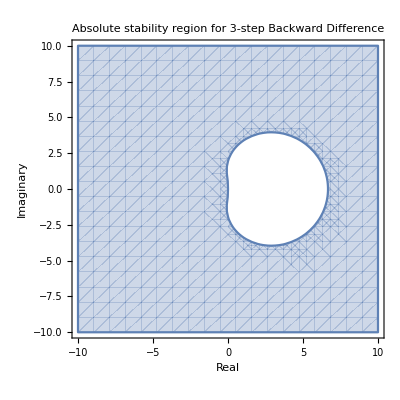

```mathematica
ComplexRegionPlot[{Abs[BDF3Roots[[1]]] <= 1&&Abs[BDF3Roots[[2]]] <= 1 && Abs[BDF3Roots[[3]]] <= 1}, {r, 10},FrameLabel->{"Real", "Imaginary"}, PlotLabel->"Absolute stability region for 3-step Backward Difference"]
```